## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGMd";
fitLabel="";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_manuscript.csv";

mainFolder = "fit_PGMd_Keq_test";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\Manuscript\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(*(626.7176791692085*0.00019)/(417.8117861128057*0.0002)
KeqList0[[1]][[3]]=1.425; (*kcat_f*km_r / kcat_r*km_f*)*)
```

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)


KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGMd[c] + 23dpg[c] <=> E_PGMd[c]&23dpg",
				"E_PGMd[c]&23dpg + 3pg[c] <=> E_PGMd[c]&23dpg&3pg",
				"E_PGMd[c]&23dpg&3pg <=> E_PGMd[c]&23dpg&2pg",
				"E_PGMd[c]&23dpg&2pg <=> E_PGMd[c]&23dpg + 2pg[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((PGMd^c)_^+(23dpg)^c⇌(PGMd^c&(23dpg)^c)_^)^PGMd1,((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,((PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c)^PGMd3,((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,Overscript[(PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c, PGMd3],((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGMd^c&(23dpg)^c&(3pg)^c)_^-((PGMd^c&(23dpg)^c&(2pg)^c)_^)/K_PGMd4) Volume_c k_PGMd4^⟶}

Volume_c (-(PGMd^c&(23dpg)^c&(2pg)^c)_^ k_PGMd4^⟵+(PGMd^c&(23dpg)^c&(3pg)^c)_^ k_PGMd4^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	23dpg[c]	2pg[c]	3pg[c]	param_PGMd_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0.0001	0	0.00002	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.09090909090909091
1	0.0001	0	0.00003169786384922229	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.13680688860321008
1	0.0001	0	0.00005023772863019165	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.2007600089131019
1	0.0001	0	0.00007962143411069939	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.2847472489508013
1	0.0001	0	0.0001261914688960386	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.38686317984685686
1	0.0001	0	0.00020000000000000004	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.5
1	0.0001	0	0.0003169786384922229	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.6131368201531432
1	0.0001	0	0.0005023772863019165	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.7152527510491988
1	0.0001	0	0.0007962143411069948	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.7992399910868982
1	0.0001	0	0.0012619146889603862	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.8631931113967899
1	0.0001	0	0.0020000000000000005	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.9090909090909091
1	0.0001	0.000018999999999999994	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.09090909090909087
1	0.0001	0.00003011297065676116	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.13680688860321003
1	0.0001	0.00004772584219868205	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.20076000891310186
1	0.0001	0.0000756403624051644	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.2847472489508012
1	0.0001	0.00011988189545123664	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.38686317984685686
1	0.0001	0.00018999999999999996	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.49999999999999994
1	0.0001	0.0003011297065676116	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.6131368201531432
1	0.0001	0.0004772584219868205	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.7152527510491987
1	0.0001	0.0007564036240516448	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.7992399910868982
1	0.0001	0.0011988189545123664	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.8631931113967899
1	0.0001	0.0018999999999999996	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.9090909090909092
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057

### Simulate data with uncertainty

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

python "C:\MASSef\python_code\src\run_fit_rel.py" "C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\psoParameters__20237122025.txt" "C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\lmaParameters__20237122025.txt" "C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\output\raw\summary__20237122025.txt" "C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\output\raw\psoResults__20237122025.txt" "C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\output\raw\lmaResults__20237122025.txt" 5 "C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\PGMd_.dat"

best_fit: 1.099050330189002
best_fit: 1.0936706298285481
best_fit: 1.0854286186604656
best_fit: 1.0782324111432255
best_fit: 1.0683250631961896

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
(*datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];*)
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | haldaneRatio_1 | 0.0871342 | 0.00759236 | 0.0419915 | 22.2177 | 0.189 | 0.230991
1 | relRateFor_3pg | 0.20419 | 0.0416937 | 0.0341001 | 37.5101 | 0.0909091 | 0.056809
1 | relRateFor_3pg | 0.195882 | 0.0383699 | 0.0496653 | 36.3032 | 0.136807 | 0.0871416
1 | relRateFor_3pg | 0.184034 | 0.0338686 | 0.0693456 | 34.5415 | 0.20076 | 0.131414
1 | relRateFor_3pg | 0.167967 | 0.0282129 | 0.0913311 | 32.0745 | 0.284747 | 0.193416
1 | relRateFor_3pg | 0.147595 | 0.0217843 | 0.111464 | 28.8123 | 0.386863 | 0.275399
1 | relRateFor_3pg | 0.123849 | 0.0153387 | 0.124058 | 24.8117 | 0.5 | 0.375942
1 | relRateFor_3pg | 0.09873 | 0.00974762 | 0.124679 | 20.3346 | 0.613137 | 0.488458
1 | relRateFor_3pg | 0.0747384 | 0.00558582 | 0.11308 | 15.8098 | 0.715253 | 0.602173
1 | relRateFor_3pg | 0.0539616 | 0.00291185 | 0.0933848 | 11.6842 | 0.79924 | 0.705855
1 | relRateFor_3pg | 0.0374462 | 0.00140222 | 0.0713088 | 8.26105 | 0.863193 | 0.791884
1 | relRateFor_3pg | 0.025194 | 0.00063474 | 0.0512371 | 5.63608 | 0.909091 | 0.857854
1 | relRateRev_2pg | 0.340683 | 0.116065 | 0.108291 | 119.121 | 0.0909091 | 0.199201
1 | relRateRev_2pg | 0.315323 | 0.0994286 | 0.145962 | 106.692 | 0.136807 | 0.282768
1 | relRateRev_2pg | 0.282287 | 0.0796862 | 0.1838 | 91.5523 | 0.20076 | 0.38456
1 | relRateRev_2pg | 0.242401 | 0.0587583 | 0.21283 | 74.7435 | 0.284747 | 0.497577
1 | relRateRev_2pg | 0.198374 | 0.0393524 | 0.223983 | 57.8972 | 0.386863 | 0.610846
1 | relRateRev_2pg | 0.154301 | 0.0238089 | 0.213298 | 42.6597 | 0.5 | 0.713298
1 | relRateRev_2pg | 0.114291 | 0.0130625 | 0.18458 | 30.1042 | 0.613137 | 0.797717
1 | relRateRev_2pg | 0.0810943 | 0.00657629 | 0.14684 | 20.5298 | 0.715253 | 0.862092
1 | relRateRev_2pg | 0.0555729 | 0.00308835 | 0.109104 | 13.6509 | 0.79924 | 0.908344
1 | relRateRev_2pg | 0.0370979 | 0.00137626 | 0.0769759 | 8.91757 | 0.863193 | 0.940169
1 | relRateRev_2pg | 0.0243071 | 0.000590837 | 0.052332 | 5.75652 | 0.909091 | 0.961423
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateFor | 0.0871314 | 0.00759188 | 113.927 | 18.1783 | 626.718 | 512.791
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644
1 | absRateRev | 0.0871375 | 0.00759294 | 92.8322 | 22.2187 | 417.812 | 510.644

### Simulated Data and Best Fit Data Plot

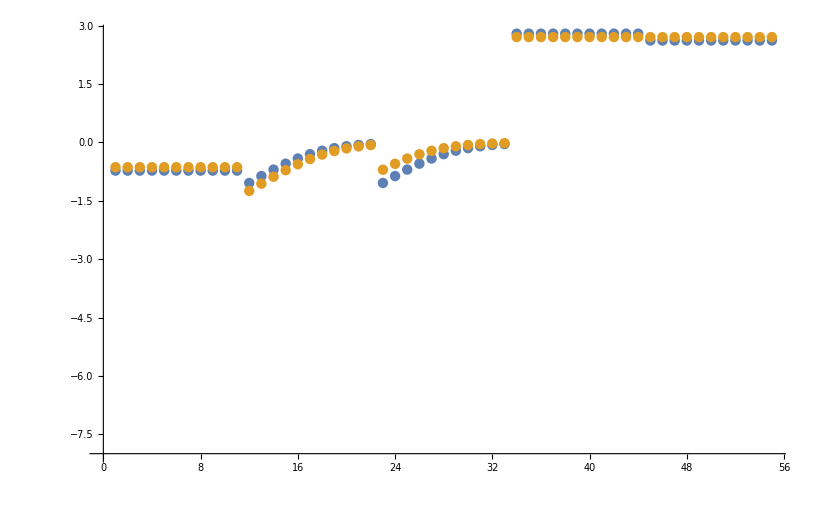

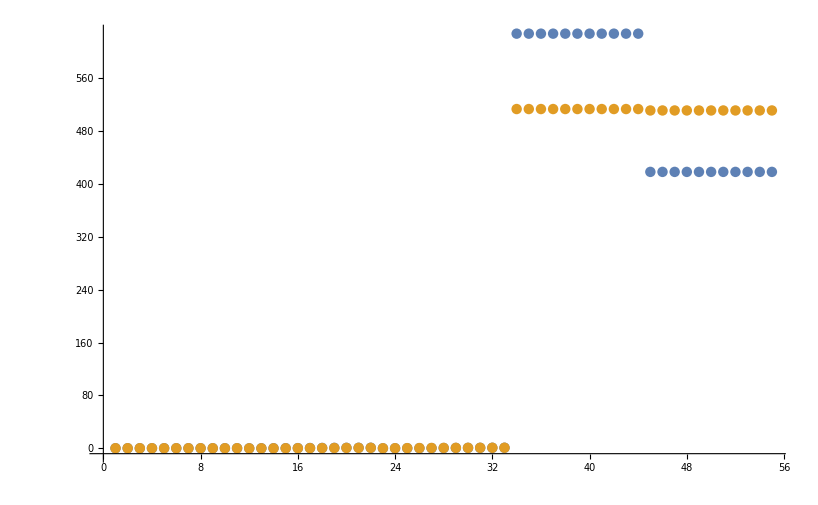

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

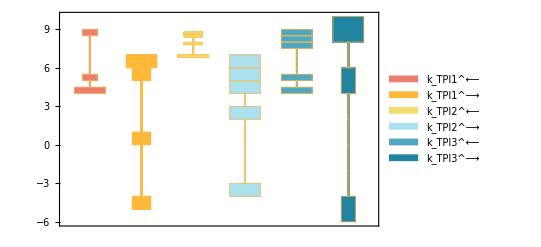

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

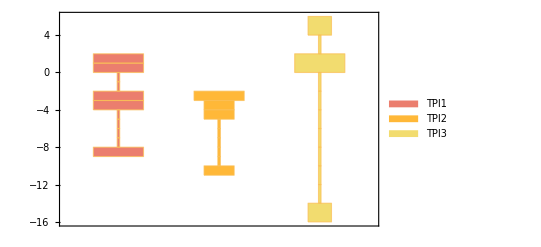

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

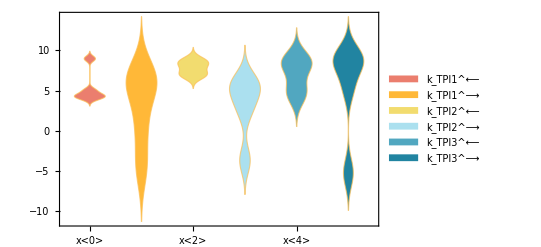

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.0002 | 0.000331954 | 65.9768
0.00019 | 0.0000763769 | 59.8016

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
626.718 | 512.791 | 18.1783
417.812 | 510.644 | 22.2187

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[All,3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
0.189 | 0.230991 | 22.2177

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

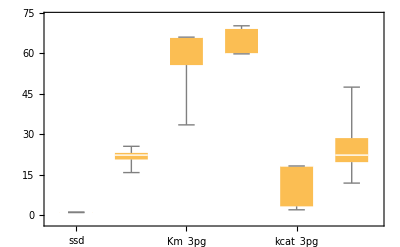

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```